Got it reasonably cleaned up in DiffGeo4, now I want to do it ALL from scratch, in theory I could put in any coordinates or metric or anything and it would run nicely. Let’s see how it goes.

```mathematica
(*Initial Conditions*)
L0 = 72/(√395);
E0 = √(217/237);
(*L0 = 3.72737;
E0 = 0.95845;*)
r0 = 7.2;
ϕ0 = 0;
t0=0;
θ0=π/2
M0 = 1;
NullOrTimelike = -1
```

π/2

-1

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Schwarzschild here) *)
f[r_]:=1-(2M)/r;
metric={{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
inverseMetric=Simplify[Inverse[metric]];
```

```mathematica
(* Set initial velocities for t and ϕ above, then find initial r-velocity from normalisation of the vector. Set null or timelike path above *)
(*u = {ut, ur, uθ, uϕ};*)
u[α_]:=D[coords[[α]][τ],τ];
metricOfτ=metric/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};
guuEq = Sum[metricOfτ[[a,b]]u[a]u[b], {a, 1, d}, {b, 1, d}];
(*ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]*)
ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, t'[τ]->-E0/f[r0], θ'[τ]->0, ϕ'[τ]->L0/r0^2, r'[τ]->r'[0]}/.M->M0
```

{r'[0]→0.102706+0. ⅈ}

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];
(* Ask Niels if this is a good way to go about it *)
(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
(* I could also use the metric[τ] I used above but this is cleaner *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==(r'[0]/.ur0), ϕ[0]==ϕ0, ϕ'[0]==L/r0^2, t[0]==0, t'[0]==-En/f[r0], θ[0]==Pi/2, θ'[0]==0}
```

{-(2 M r'[τ] t'[τ])/(2 M r[τ]-r[τ]^2)+t''[τ]==0,(M r'[τ]^2)/(2 M r[τ]-r[τ]^2)+(M (-2 M+r[τ]) t'[τ]^2)/r[τ]^3+(2 M-r[τ]) θ'[τ]^2+(2 M-r[τ]) Sin[θ[τ]]^2 ϕ'[τ]^2+r''[τ]==0,(2 r'[τ] θ'[τ])/r[τ]-Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2+θ''[τ]==0,(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ[τ]] θ'[τ] ϕ'[τ]+ϕ''[τ]==0,r[0]==7.2,r'[0]==0.102706+0. ⅈ,ϕ[0]==0,ϕ'[0]==0.0192901 L,t[0]==0,t'[0]==-En/(1-0.277778 M),θ[0]==π/2,θ'[0]==0}

```mathematica
solRange=2000;
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

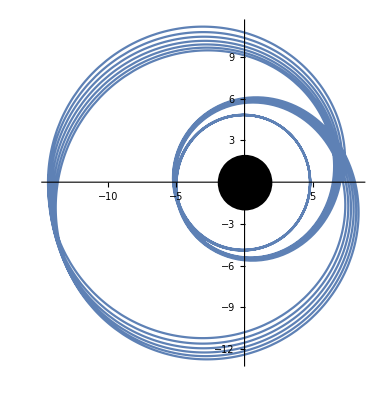

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

```mathematica
(* Frequency stuff *)
tIntegrand=(1/(p-2-2e Cos[χprime]))(1/(1+e Cos[χprime])^2)(1/(√(p-6-2e Cos[χprime])))

t[χ_, p_, e_]:=p^2 M√(p-2-2e) √(p-2+2e)NIntegrate[1/(p-2-2e Cos[χprime]) 1/(1+e Cos[χprime])^2 1/(√(p-6-2e Cos[χprime]))/.M->1,{χprime, 0, χ}]
```

1/(√(4.-1. Cos[χprime]) (8.-1. Cos[χprime]) (1+0.5 Cos[χprime])^2)

```mathematica
e=0.5
pOffset=3
p=6+2e+pOffset
t[2π, p, e]
```

0.5

3

10.

433.901